```mathematica
m1c=Import["/Users/benxgh1996/Desktop/Zeeman/data.xlsx",{"Data",1,Range[3,15],{2,3}}]
```

{{0.,0.004},{0.936,0.057},{1.711,0.104},{2.545,0.154},{3.342,0.202},{4.089,0.247},{4.98,0.301},{5.791,0.348},{6.561,0.393},{7.38,0.443},{8.23,0.491},{8.98,0.531},{9.77,0.57}}

```mathematica
m2c=Import["/Users/benxgh1996/Desktop/Zeeman/data.xlsx",{"Data",1,Range[3,15],{6,7}}]
```

{{0.,0.004},{0.944,0.061},{1.778,0.112},{2.58,0.161},{3.348,0.207},{4.127,0.254},{4.994,0.306},{5.81,0.355},{6.61,0.403},{7.43,0.451},{8.19,0.495},{8.96,0.536},{9.84,0.571}}

```mathematica
FindFit[m1c,a x+b,{a,b},x]
```

{a→0.0587193,b→0.00526677}

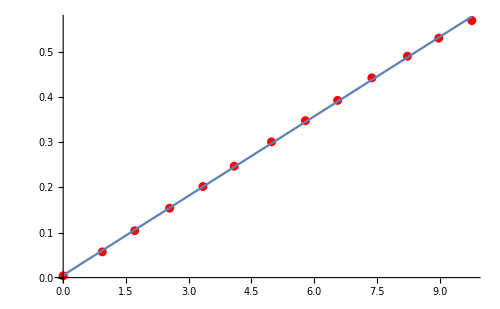

```mathematica
Show[ListPlot[m1c,PlotStyle->Red],Plot[a x+b/.{a->0.05871930288501721,b->0.0052667719192397554},{x,0.,9.77}]]
```

```mathematica
FindFit[m2c, a x+b,{a,b},x]
```

{a→0.0587877,b→0.00905126}

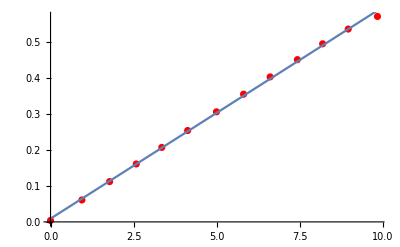

```mathematica
Show[ListPlot[m2c,PlotStyle->Red],Plot[a x+b/.{a->0.058787723345170594,b->0.009051262072706602},{x,0.,9.84}]]
```

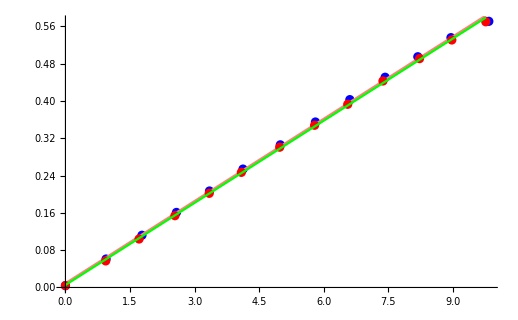

```mathematica
Show[ListPlot[m2c,PlotStyle->Blue],Plot[a x+b/.{a->0.058787723345170594,b->0.009051262072706602},{x,0.,9.84},PlotStyle->Pink],ListPlot[m1c,PlotStyle->Red],Plot[a x+b/.{a->0.05871930288501721,b->0.0052667719192397554},{x,0.,9.77},PlotStyle->Green]]
```

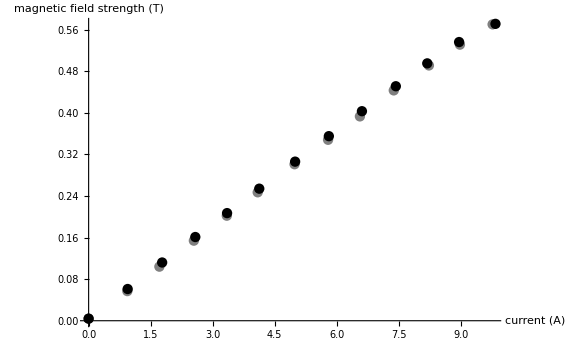

```mathematica
Show[ListPlot[m1c,PlotStyle->Gray],ListPlot[m2c,PlotStyle->Black],AxesLabel-> {"current (A)","magnetic field strength (T)"},BaseStyle->{FontSize->14}]
```

```mathematica
mag[current_]:=a*current+b/.{a->0.05871930288501721,b->0.0052667719192397554}
```

```mathematica
mag[6.60]
```

0.392814

```mathematica
mag[8.16]
```

0.484416

```mathematica
{First@#, mag[First@#]}&/@m1c
```

{{0.,0.00526677},{0.936,0.060228},{1.711,0.105735},{2.545,0.154707},{3.342,0.201507},{4.089,0.24537},{4.98,0.297689},{5.791,0.34531},{6.561,0.390524},{7.38,0.438615},{8.23,0.488527},{8.98,0.532566},{9.77,0.578954}}

```mathematica
mct=Join[m1c,m2c]
```

{{0.,0.004},{0.936,0.057},{1.711,0.104},{2.545,0.154},{3.342,0.202},{4.089,0.247},{4.98,0.301},{5.791,0.348},{6.561,0.393},{7.38,0.443},{8.23,0.491},{8.98,0.531},{9.77,0.57},{0.,0.004},{0.944,0.061},{1.778,0.112},{2.58,0.161},{3.348,0.207},{4.127,0.254},{4.994,0.306},{5.81,0.355},{6.61,0.403},{7.43,0.451},{8.19,0.495},{8.96,0.536},{9.84,0.571}}

```mathematica
FindFit[mct,a x+b,{a,b},x]
```

{a→0.0587561,b→0.00714679}

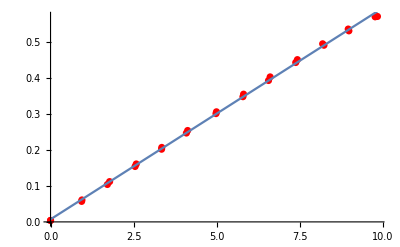

```mathematica
Show[ListPlot[mct,PlotStyle->Red],Plot[a x+b/.{a->0.0587560564825241,b->0.007146794689772938},{x,0.,9.84}]]
```

```mathematica
l={1,2,3,4,5}
```

{1,2,3,4,5}

```mathematica
l[[1;;-1]]
```

{1,2,3,4,5}

```mathematica
FindFit[m1c[[1;;-2]],a x+b,{a,b},x]
```

{a→0.0592146,b→0.00376179}

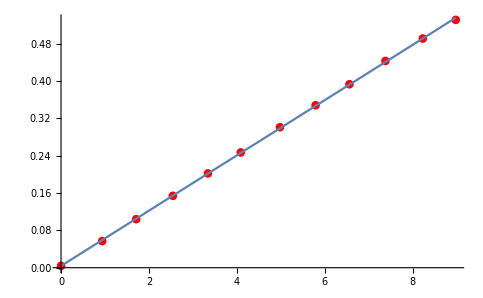

```mathematica
Show[ListPlot[m1c⟦1;;-2⟧,PlotStyle->Red],Plot[a x+b/.{a->0.05921456721539378,b->0.0037617859363623407},{x,0.,8.98}]]
```

```mathematica
k=2*(4*10^-3)*√(1.4568^2-1)*(9.274*10^-24)/((6.626*10^-34)*(2.9979*10^8))
```

0.395673

```mathematica
kHg=2*(4*10^-3)*√(1.4602^2-1)*(9.274*10^-24)/((6.626*10^-34)*(2.9979*10^8))
```

0.397418

```mathematica
r1d=Import["/Users/benxgh1996/Desktop/Zeeman/data.xlsx",{"Data",2,Range[2,8],{6,2}}]
```

{{0.119672,5.206},{0.160656,6.036},{0.167213,6.76},{0.214754,7.53},{0.218033,8.3},{0.221311,9.},{0.245902,9.77}}

```mathematica
rbd={mag[Last@#],First@#}&/@r1d
```

{{0.310959,0.119672},{0.359696,0.160656},{0.402209,0.167213},{0.447423,0.214754},{0.492637,0.218033},{0.53374,0.221311},{0.578954,0.245902}}

```mathematica
FindFit[rbd,a x,a,x]
```

{a→0.431653}

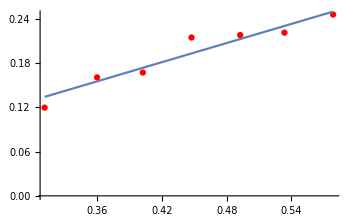

```mathematica
Show[ListPlot[rbd,PlotStyle->Red],Plot[a x/.{a->0.43165346019726036},{x,0.3109594627386394,0.5789543611058579}]]
```

```mathematica
a/k/.{a->0.43165346019726036}
```

1.09093

```mathematica
r1dt=Import["/Users/benxgh1996/Desktop/Zeeman/data.xlsx",{"Data",2,Range[2,12],{2,6}}]
```

{{5.206,0.119672},{6.036,0.160656},{6.76,0.167213},{7.53,0.214754},{8.3,0.218033},{9.,0.221311},{9.77,0.245902},{5.204,0.136066},{6.004,0.190164},{6.77,0.160656},{6.067,0.118033}}

```mathematica
rbdt={mag[First@#],Last@#}&/@r1dt
```

{{0.310959,0.119672},{0.359696,0.160656},{0.402209,0.167213},{0.447423,0.214754},{0.492637,0.218033},{0.53374,0.221311},{0.578954,0.245902},{0.310842,0.136066},{0.357817,0.190164},{0.402796,0.160656},{0.361517,0.118033}}

```mathematica
p1=#[[2]]/#[[1]]&/@rbdt
```

{0.384848,0.446643,0.415737,0.47998,0.442583,0.414642,0.424734,0.437732,0.531455,0.398851,0.326493}

```mathematica
Mean[p1]
```

0.427609

```mathematica
StandardDeviation[p1]
```

0.0523574

```mathematica
FindFit[rbdt,a x,a,x]
```

{a→0.428757}

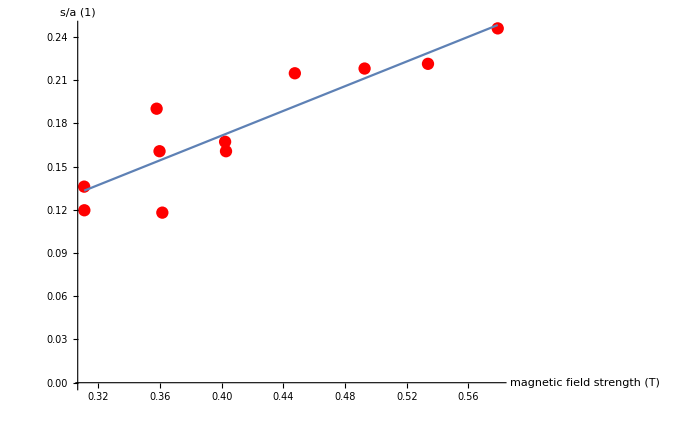

```mathematica
Show[ListPlot[rbdt,PlotStyle->Red],Plot[a x/.{a->0.4287573863475642},{x,0.3108420241328693,0.5789543611058579}],AxesLabel-> {"magnetic field strength (T)", "s/a (1)"},BaseStyle->{FontSize->14}]
```

```mathematica
a/k/.{a->0.4287573863475642}
```

1.08362

```mathematica
r2d=Import["/Users/benxgh1996/Desktop/Zeeman/data.xlsx",{"Data",3,Range[2,9],{2,6}}]
```

{{4.151,0.059375},{5.,0.090625},{5.816,0.121875},{6.56,0.164063},{7.43,0.192187},{8.12,0.201562},{8.84,0.220312},{9.62,0.23125}}

```mathematica
rb2d={mag[First@#],Last@#}&/@r2d
```

{{0.249011,0.059375},{0.298863,0.090625},{0.346778,0.121875},{0.390465,0.164063},{0.441551,0.192187},{0.482068,0.201562},{0.524345,0.220312},{0.570146,0.23125}}

```mathematica
p2=#[[2]]/#[[1]]&/@rb2d
```

{0.238444,0.303232,0.351449,0.420172,0.435255,0.418121,0.420167,0.405598}

```mathematica
StandardDeviation[p2]
```

0.0705616

```mathematica
Mean[p2]
```

0.374055

```mathematica
0.0705615791987829/0.4
```

0.176404

```mathematica
FindFit[rb2d,a x,a,x]
```

{a→0.39795}

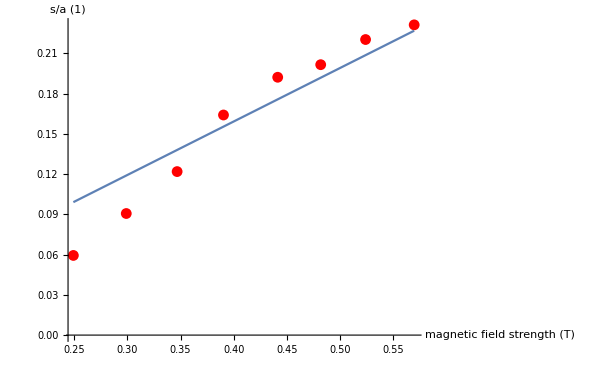

```mathematica
Show[ListPlot[rb2d,PlotStyle->Red],Plot[a x/.{a->0.39795037618285406},{x,0.2490105981949462,0.5701464656731053}],AxesLabel-> {"magnetic field strength (T)", "s/a (1)"},BaseStyle->{FontSize->14}]
```

```mathematica
a/k/.{a->0.39795037618285406}
```

1.00576

```mathematica
g1d=Import["/Users/benxgh1996/Desktop/Zeeman/data.xlsx",{"Data",4,Range[2,7],{2,6}}]
```

{{4.994,0.147826},{5.78,0.171739},{6.594,0.202174},{7.4,0.247826},{8.13,0.28913},{8.86,0.315217}}

```mathematica
gb1d={mag[First@#],Last@#}&/@g1d
```

{{0.298511,0.147826},{0.344664,0.171739},{0.392462,0.202174},{0.43979,0.247826},{0.482655,0.28913},{0.52552,0.315217}}

```mathematica
p3=#[[2]]/#[[1]]&/@gb1d
```

{0.495212,0.498279,0.515143,0.563511,0.599042,0.59982}

```mathematica
Mean[p3]
```

0.545168

```mathematica
StandardDeviation[p3]
```

0.0486239

```mathematica
FindFit[gb1d,a x, a,x]
```

{a→0.560711}

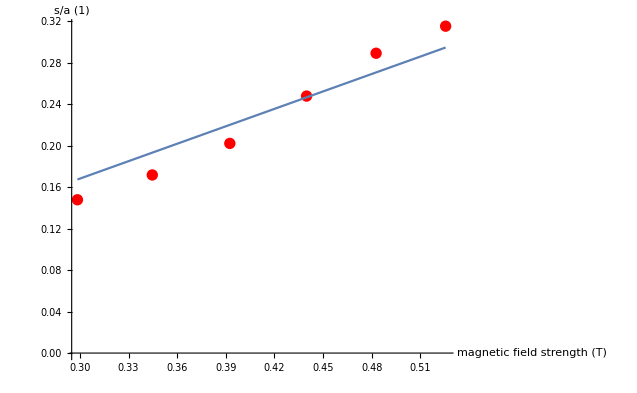

```mathematica
Show[ListPlot[gb1d,PlotStyle->Red],Plot[a x/.{a->0.56071097962971},{x,0.2985109705270157,0.5255197954804922}],AxesLabel-> {"magnetic field strength (T)", "s/a (1)"},BaseStyle->{FontSize->14}]
```

```mathematica
kHg*3/2
```

0.596126

```mathematica
a/(kHg*3/2)/.{a->0.56071097962971}
```

0.940591

```mathematica
1-%
```

0.0594091

```mathematica
a/kHg/.{a->0.56071097962971}
```

1.41089

```mathematica
$Assumptions=λ>0&&d>0&&m>0&&m∈Integers
```

λ>0&&d>0&&m>0&&m∈Integers

```mathematica
A[m_]:=m*(1+1/2 m^2*λ^2/d^2)
```

```mathematica
A[m]-A[m-1]
```

-(-1+m) (1+((-1+m)^2 λ^2)/(2 d^2))+m (1+(m^2 λ^2)/(2 d^2))

```mathematica
Simplify[-(-1+m) (1+((-1+m)^2 λ^2)/(2 d^2))+m (1+(m^2 λ^2)/(2 d^2))]
```

(2 d^2+(1-3 m+3 m^2) λ^2)/(2 d^2)

```mathematica
Table[(2 d^2+(1-3 m+3 m^2) λ^2)/(2 d^2),{m,1,20}]/.{d-> 4*10^-3,λ-> 644*10^-9}
```

```mathematica
N[{2000000025921/2000000000000,2000000181447/2000000000000,2000000492499/2000000000000,2000000959077/2000000000000,2000001581181/2000000000000,2000002358811/2000000000000,2000003291967/2000000000000,2000004380649/2000000000000,2000005624857/2000000000000,2000007024591/2000000000000,2000008579851/2000000000000,2000010290637/2000000000000,2000012156949/2000000000000,2000014178787/2000000000000,2000016356151/2000000000000,2000018689041/2000000000000,2000021177457/2000000000000,2000023821399/2000000000000,2000026620867/2000000000000,2000029575861/2000000000000}]
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001}

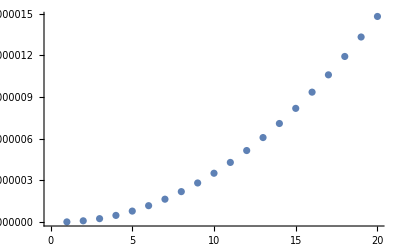

```mathematica
ListPlot[%7]
```

```mathematica
Table[ArcCos[√(n^2-m^2*(λ/(2d))^2)]*360/(2π),{m,13163,13163+20}]/.{d-> 4*10^-3,λ-> 643.85*10^-9,n-> 1.4568}
```

{0.167062,0.766648,1.0713,1.30681,1.50596,1.68172,1.8408,1.98721,2.12358,2.25173,2.37299,2.48837,2.59865,2.70446,2.8063,2.90459,2.99968,3.09187,3.1814,3.26849,3.35334}

```mathematica
Table[ArcCos[√(n^2-m^2*(λ/(2d))^2)],{m,13163,13163+20}]/.{d-> 4*10^-3,λ-> 643.85*10^-9,n-> 1.4568}
```

{0.00291578,0.0133805,0.0186978,0.0228081,0.0262839,0.0293515,0.032128,0.0346834,0.0370635,0.0393001,0.0414165,0.0434303,0.045355,0.0472018,0.0489792,0.0506947,0.0523543,0.0539633,0.0555259,0.057046,0.0585269}

```mathematica
Tan[#]&/@%48
```

{0.00291579,0.0133813,0.0187,0.022812,0.0262899,0.0293599,0.032139,0.0346973,0.0370805,0.0393203,0.0414402,0.0434576,0.0453862,0.0472368,0.0490184,0.0507382,0.0524022,0.0540157,0.055583,0.0571079,0.0585938}

```mathematica
Table[Tan[ArcCos[√(n^2-m^2*(λ/(2d))^2)]],{m,13163,13163+20}]/.{d-> 4*10^-3,λ-> 643.85*10^-9,n-> 1.4568}
```

{0.00291579,0.0133813,0.0187,0.022812,0.0262899,0.0293599,0.032139,0.0346973,0.0370805,0.0393203,0.0414402,0.0434576,0.0453862,0.0472368,0.0490184,0.0507382,0.0524022,0.0540157,0.055583,0.0571079,0.0585938}

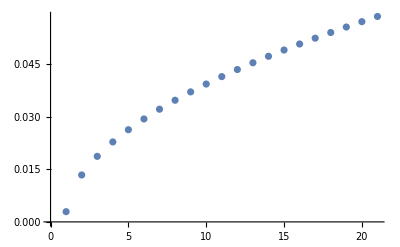

```mathematica
ListPlot[%33]
```

```mathematica
tanList=%33
```

{0.00291579,0.0133813,0.0187,0.022812,0.0262899,0.0293599,0.032139,0.0346973,0.0370805,0.0393203,0.0414402,0.0434576,0.0453862,0.0472368,0.0490184,0.0507382,0.0524022,0.0540157,0.055583,0.0571079,0.0585938}

```mathematica
list={}
```

{}

```mathematica
i
```

1

```mathematica
For[i=1,i<Length[%33],i++,
AppendTo[list,tanList[[i+1]]-tanList[[i]]]]
```

```mathematica
list
```

{0.0104655,0.00531865,0.00411207,0.0034779,0.00306996,0.00277914,0.00255827,0.00238315,0.00223988,0.00211985,0.00201739,0.00192859,0.00185067,0.00178158,0.00171977,0.00166404,0.00161347,0.0015673,0.00152493,0.00148587}

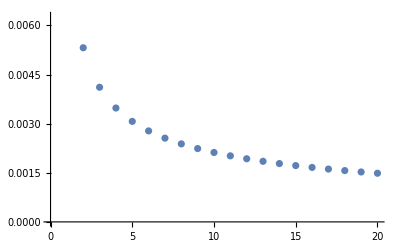

```mathematica
ListPlot[%41]
```

```mathematica
Table[√(n^2-m^2*(λ/(2d))^2),{m,13163,13183}]/.{d-> 4*10^-3,λ-> 643.85*10^-9,n-> 1.4568}
```

{0.999996,0.99991,0.999825,0.99974,0.999655,0.999569,0.999484,0.999399,0.999313,0.999228,0.999142,0.999057,0.998972,0.998886,0.998801,0.998715,0.99863,0.998544,0.998459,0.998373,0.998288}

```mathematica
ArcCos[1.4567999977768975]
```

0.+0.922738 ⅈ

```mathematica
Solve[n^2-m^2*(λ/(2d))^2==1,m]/.{d-> 4*10^-3,λ-> 643.85*10^-9,n-> 1.4568}
```

{{m→-13163.},{m→13163.}}

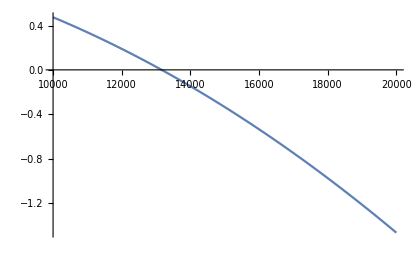

```mathematica
Plot[n^2-m^2*(λ/(2d))^2-1/.{d-> 4*10^-3,λ-> 643.85*10^-9,n-> 1.4568},{m,10000,20000}]
```

```mathematica
f[x_]:=ⅇ^x
```

```mathematica
D[f[x],x]
```

ⅇ^x

```mathematica
D[f[#],#]&[5]
```

General::ivar: 5 is not a valid variable.

∂_5 ⅇ^5

```mathematica
df[x_,dx_]:=(D[f[#],#]&[x_])*dx
```

RuleDelayed::rhs: Pattern x_ appears on the right-hand side of rule df[x_,dx_]:>(∂_#1 f[#1]&)[x_] dx.

```mathematica
df[y,dx]
```

dx ⅇ^y

```mathematica
rf[x_,dx_]:=(f[x+dx]-f[x])/df[x,dx]
```

```mathematica
rf[z,dx]
```

(ⅇ^-z (-ⅇ^z+ⅇ^(dx+z)))/dx

```mathematica
df[5,2]
```

General::ivar: 5 is not a valid variable.

2 ∂_5 ⅇ^5

```mathematica
rf[1,dx]
```

General::ivar: 1 is not a valid variable.

(-ⅇ+ⅇ^(1+dx))/(dx ∂_1 ⅇ)

```mathematica
rf[x,2]
```

1/2 ⅇ^-x (-ⅇ^x+ⅇ^(2+x))

```mathematica
N[(-ⅇ^2+ⅇ^3)/ⅇ^2]
```

1.71828

```mathematica
N[(-ⅇ^20+ⅇ^21)/ⅇ^20]
```

1.71828

```mathematica
N[(-ⅇ^200000+ⅇ^200001)/ⅇ^200000]
```

1.718281828

```mathematica
N[(-ⅇ^20000+ⅇ^20001)/ⅇ^20000]
```

1.7182818285

```mathematica
f[20001]-f[20000]
```

-ⅇ^20000+ⅇ^20001

```mathematica
N[-ⅇ^20000+ⅇ^20001]
```

1.3327001982×10^8686

```mathematica
df[20000,1]
```

ⅇ^20000

```mathematica
N[ⅇ^20000]
```

7.756004726×10^8685

```mathematica
(%102)/(%104)
```

1.7182818285

```mathematica
N[12002600100000/600130003]
```

20000.

```mathematica
(f[20002]-f[20000])/(f[20001]-f[20000])
```

1200320014/600130003

```mathematica
N[1200320014/600130003]
```

2.0001

```mathematica
(1+0.001)^100
```

1.10512

```mathematica
1+100*0.001
```

1.1

```mathematica
Sin[10000+5]-Sin[10000]
```

-Sin[10000]+Sin[10005]

```mathematica
N[-Sin[10000]+Sin[10005]]
```

1.13197

```mathematica
Cos[10000]*5
```

5 Cos[10000]

```mathematica
N[5 Cos[10000]]
```

-4.76078

```mathematica
Table[ArcCos[√(n^2-m^2*(λ/(2d))^2)],{m,15588,15588+20}]/.{d-> 4*10^-3,λ-> 546.1*10^-9,n-> 1.4602}
```

{0.008566,0.0147874,0.0190783,0.0225682,0.0255868,0.0282855,0.0307486,0.0330289,0.035162,0.0371732,0.0390813,0.0409008,0.042643,0.044317,0.0459303,0.0474891,0.0489985,0.0504631,0.0518865,0.0532722,0.0546229}

```mathematica
Solve[n^2-m^2*(λ/(2d))^2==1,m]/.{d-> 4*10^-3,λ-> 546.1*10^-9,n-> 1.4602}
```

{{m→-15587.5},{m→15587.5}}